```mathematica
R=5
v=0.5
ω = Pi/15
```

5

0.5

π/15

```mathematica
XFixed[t_]=-R+v t
YFixed[t_]=0
XRotating[t_]=XFixed[t]*Cos[ω t]
YRotating[t_]=-XFixed[t]*Sin[ω t]
```

-5+0.5 t

0

(-5+0.5 t) Cos[(π t)/15]

(5-0.5 t) Sin[(π t)/15]

```mathematica
Animate[Show[ParametricPlot[{XRotating[t], YRotating[t]}, {t,0,10}],Graphics[{Green,Disk[{0,0},R],Red, PointSize[0.05], Point[{XRotating[T], YRotating[T]}]}]],{T,0,10}]
```

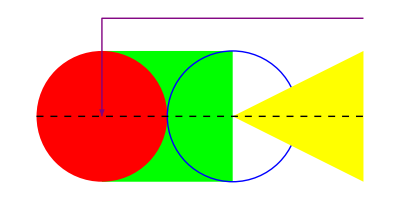

```mathematica
Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]
```

```mathematica
rot =Animate[Show[Graphics[{RGBColor["#49beb7"],Disk[{0,0},R],Blue,Arrowheads[Large],Arrow[{{0,0},{2,0}}],RGBColor["#118df0"],Arrowheads[Large],Arrow[{{0,0},{0,2}}]}],ParametricPlot[{XRotating[t], YRotating[t]}, {t,0,20}], Graphics[{RGBColor["#ff304f"], PointSize[0.05],Point[{XRotating[T], YRotating[T]}]}]],{T,0,20}]
```

```mathematica
fix=Animate[Show[Graphics[{RGBColor["#49beb7"],Disk[{0,0},R],Blue,Arrowheads[Large],Arrow[{{0,0},{ 2Cos[ω T], 2Sin[ω T]}}],RGBColor["#118df0"],Arrowheads[Large],Arrow[{{0,0},{ -2Sin[ω T], 2Cos[ω T]}}]}],ParametricPlot[{XFixed[t], YFixed[t]}, {t,0,20}], Graphics[{RGBColor["#ff304f"], PointSize[0.05],Point[{XFixed[T], YFixed[T]}]}]],{T,0,20}]
```

```mathematica
graph=Table[Column[{Show[Graphics[{RGBColor["#49beb7"],Disk[{0,0},R],Blue,Arrowheads[Large],Arrow[{{0,0},{ 2Cos[ω T], 2Sin[ω T]}}],RGBColor["#118df0"],Arrowheads[Large],Arrow[{{0,0},{ -2Sin[ω T], 2Cos[ω T]}}]}],ParametricPlot[{XFixed[t], YFixed[t]}, {t,0,20}], Graphics[{RGBColor["#ff304f"], PointSize[0.05],Point[{XFixed[T], YFixed[T]}]}]],Show[Graphics[{RGBColor["#49beb7"],Disk[{0,0},R],Blue,Arrowheads[Large],Arrow[{{0,0},{2,0}}],RGBColor["#118df0"],Arrowheads[Large],Arrow[{{0,0},{0,2}}]}],ParametricPlot[{XRotating[t], YRotating[t]}, {t,0,20}], Graphics[{RGBColor["#ff304f"], PointSize[0.05],Point[{XRotating[T], YRotating[T]}]}]]}],{T,0,20,0.4}];
```

```mathematica
Export["graph3.gif",graph, ImageSize->{400,800},ImageResolution->200]
```

graph3.gif